#### Spectra analysis

```mathematica
Sigma[1]={{0,1},{1,0}}
Sigma[2]={{0,-I},{I,0}}
Sigma[3]={{1,0},{0,-1}}
```

{{0,1},{1,0}}

{{0,-ⅈ},{ⅈ,0}}

{{1,0},{0,-1}}

```mathematica
Tensor[M1_,M2_]:=ArrayFlatten[Table[M1[[i,j]]*M2, {i, 1,Length[M1[[1]]]}, {j, 1, Length[M1[[1]]]}]]
```

```mathematica
Tensor[Sigma[1],Sigma[2]]//MatrixForm
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

```mathematica
Sigma[j_,k_]:=If[j==1,Tensor[Sigma[k],IdentityMatrix[2^5]],Tensor[Tensor[IdentityMatrix[2^(j-1)],Sigma[k]],IdentityMatrix[2^(6-j)]]]
```

```mathematica
(* Sigma[j_,k_]:=If[j==1,Tensor[Sigma[k],IdentityMatrix[2^2]],Tensor[Tensor[IdentityMatrix[2^(j-1)],Sigma[k]],IdentityMatrix[2^(3-j)]]] *)
```

```mathematica
Length[MatrixForm[Sigma[1,1]]]
```

1

```mathematica
Length[Sigma[2,1]]
```

64

```mathematica
Tr[Sigma[2,1].Sigma[2,1]]
```

64

```mathematica
Sigma[1]
```

{{0,1},{1,0}}

```mathematica
Ham1[l_]:= Sigma[l,1].Sigma[l+3,1]+Sigma[l,2].Sigma[l+3,2];
```

```mathematica
H1=Ham1[1]+Ham1[2]+Ham1[3];
```

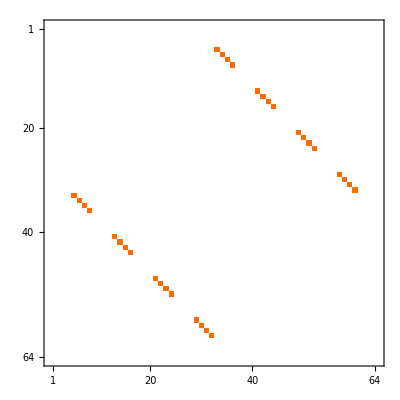
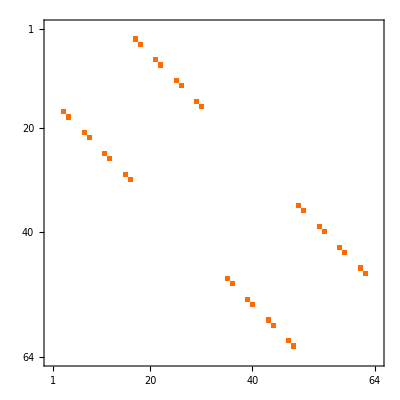
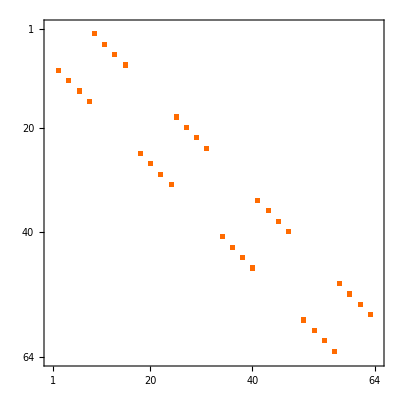
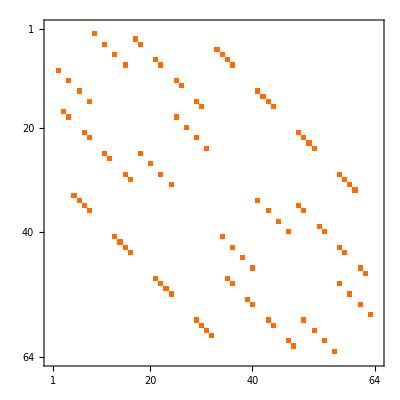

```mathematica
{MatrixPlot[Ham1[1]],MatrixPlot[Ham1[2]],MatrixPlot[Ham1[3]],MatrixPlot[H1]}
```

```mathematica
Sigmap[l_]:= (Sigma[l,1]+I Sigma[l,2])/2;
```

```mathematica
Sigmam[l_]:= (Sigma[l,1]-I Sigma[l,2])/2;
```

```mathematica
Pla2= Sigmap[1].Sigmap[2].Sigmap[3]+Sigmam[1].Sigmam[2].Sigmam[3];
```

```mathematica
Pla= Sigmap[1].Sigmap[2].Sigmap[3]+ Sigmap[4].Sigmap[5].Sigmap[6]+Sigmam[1].Sigmam[2].Sigmam[3]+ Sigmam[4].Sigmam[5].Sigmam[6];
```

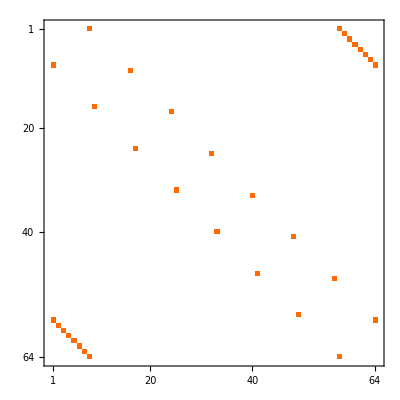

```mathematica
MatrixPlot[Pla]
```

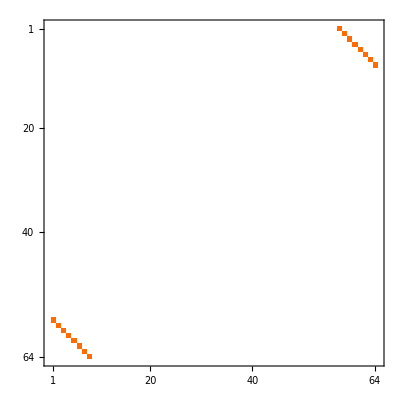

```mathematica
MatrixPlot[Pla2]
```

```mathematica
El=Sigma[1,3].Sigma[4,3]+Sigma[2,3].Sigma[5,3]+Sigma[3,3].Sigma[6,3];
```

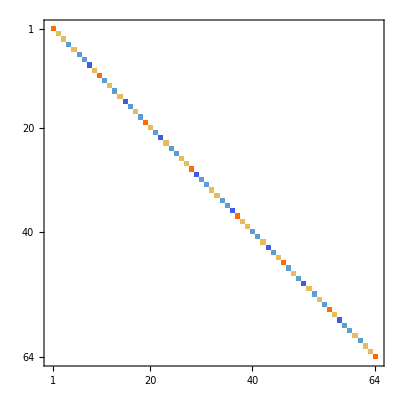

```mathematica
MatrixPlot[El]
```

```mathematica
Ht[a_,b_,c_]:=a H1+b El +c Pla
```

```mathematica
Qel1= Sigma[1,3]+Sigma[4,3]-Sigma[2,3]-Sigma[5,3];
```

```mathematica
F[a_,b_,c_]:=Eigenvalues[ a H1+b El +c Pla]
```

```mathematica
MatrixPlot[Qel1.Ht[a,b,c]-Ht[a,b,c].Qel1]
```

-Graphics-

```mathematica
Eigenvalues[Qel1]
```

{-4,-4,-4,-4,4,4,4,4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Qel2= Sigma[1,3]+Sigma[4,3]-Sigma[3,3]-Sigma[6,3];
```

```mathematica
Eigenvalues[Qel2]
```

{-4,-4,-4,-4,4,4,4,4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
F[-1,0,0]
```

{-6,6,-4,-4,-4,-4,-4,-4,4,4,4,4,4,4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Eigenvalues[Ham1[1]]
```

{-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
S=IdentityMatrix[64];
```

```mathematica
Pro1= (Qel1+4 S).(Qel1-4 S).(Qel1+2S).(Qel1-2S)/64;
```

```mathematica
Pro2=(Qel2+4S).(Qel2-4S).(Qel2+2S).(Qel2-2S)/64;
```

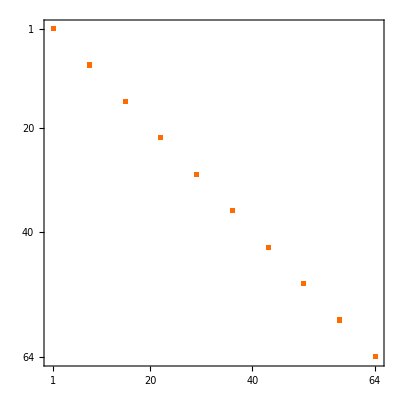
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[Pro1.Pro2],MatrixPlot[Pro2.Pro1],MatrixPlot[Pro1.Pro2-Pro2.Pro1]}
```

```mathematica
Eigenvalues[N[Pro1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Eigenvalues[N[Pro1.Pro2]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
F[-1,0,0]
```

{-6,6,-4,-4,-4,-4,-4,-4,4,4,4,4,4,4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

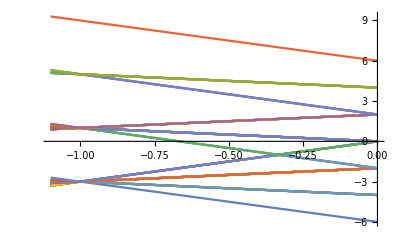

```mathematica
ListPlot[Transpose[Table[Sort[F[-1,a,0],Less],{a,-1.1,0,0.025}]],Joined->True,DataRange->{-1.1,0}]
```

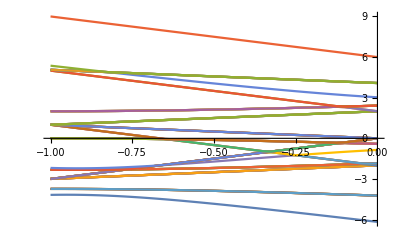

```mathematica
ListPlot[Transpose[Table[Sort[F[-1,a,-1],Less],{a,-1,0,0.025}]],Joined->True,DataRange->{-1,0}]
```

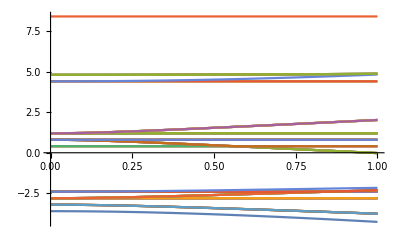

```mathematica
ListPlot[Transpose[Table[Sort[F[-1,-0.8,a],Less],{a,0,1,0.025}]],Joined->True,DataRange->{0,1}]
```

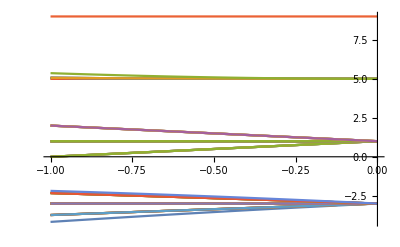

```mathematica
ListPlot[Transpose[Table[Sort[F[-1,-1,a],Less],{a,-1,0,0.025}]],Joined->True,DataRange->{-1,0}]
```

```mathematica
Sort[F[-1,-1,0],Less]
```

{-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,5,5,5,5,5,5,5,5,9}

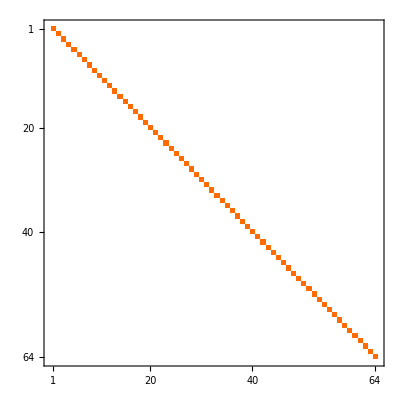

```mathematica
MatrixPlot[S]
```

```mathematica
G1=NullSpace[S-Pro1.Pro2];
```

```mathematica
Length[G1[[1]]]
```

64

```mathematica
MatrixForm[G1]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
HamRed[a_,b_,c_]:=Table[G1[[i]].(a  H1+b  El +c  Pla).G1[[j]],{i,10},{j,10}];
```

```mathematica
G1[[2]].(a  H1+b  El +c  Pla).G1[[10]]
```

c

```mathematica
Specgi[a_,b_,c_]:=Sort[Eigenvalues[HamRed[a,b,c]],Greater];
```

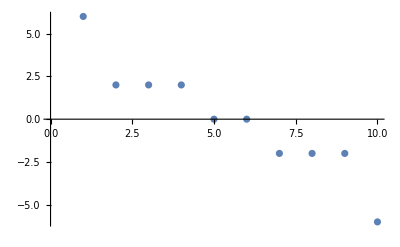

```mathematica
ListPlot[Specgi[-1,0,0]]
```

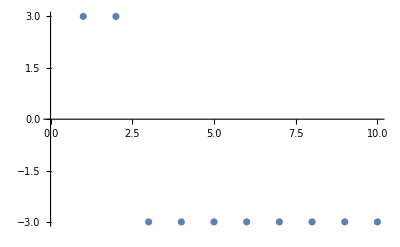

```mathematica
ListPlot[Specgi[0,+1,0]]
```

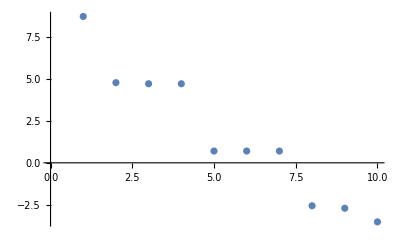

```mathematica
ListPlot[Specgi[-1,-0.9,0.4]]
```

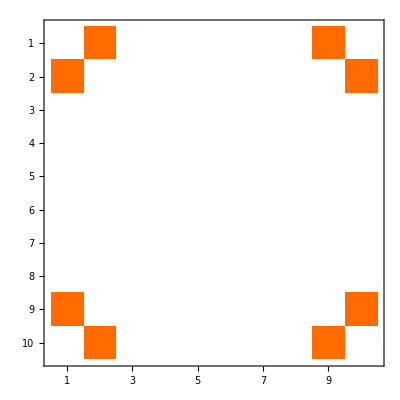

```mathematica
MatrixPlot[HamRed[0,0,1]]
```

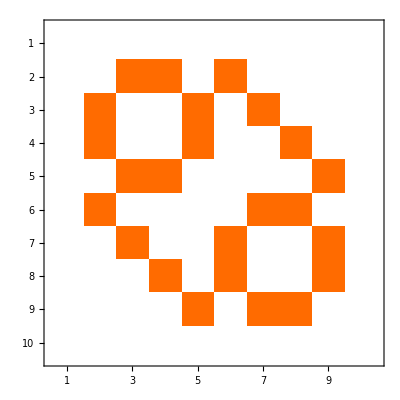

```mathematica
MatrixPlot[HamRed[1,0,0]]
```

```mathematica
MatrixForm[HamRed[0,-1,0]]
```

(-3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3)

```mathematica
MatrixForm[HamRed[-1,-1,0]]
```

(-3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | -2 | -2 | 0 | -2 | 0 | 0 | 0 | 0
0 | -2 | 3 | 0 | -2 | 0 | -2 | 0 | 0 | 0
0 | -2 | 0 | 3 | -2 | 0 | 0 | -2 | 0 | 0
0 | 0 | -2 | -2 | 3 | 0 | 0 | 0 | -2 | 0
0 | -2 | 0 | 0 | 0 | 3 | -2 | -2 | 0 | 0
0 | 0 | -2 | 0 | 0 | -2 | 3 | 0 | -2 | 0
0 | 0 | 0 | -2 | 0 | -2 | 0 | 3 | -2 | 0
0 | 0 | 0 | 0 | -2 | 0 | -2 | -2 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3)

```mathematica
G2=NullSpace[3*IdentityMatrix[10]+HamRed[-1,-1,0]];
```

```mathematica
G2t=G2*{1,1/Sqrt[8],1}
```

{{0,0,0,0,0,0,0,0,0,1},{0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0},{1,0,0,0,0,0,0,0,0,0}}

```mathematica
Leff=Table[G2t[[i]].HamRed[a,b,c].G2t[[j]],{i,3},{j,3}]
```

{{3 b,c/(√2),0},{c/(√2),3 b,c/(√2)},{0,c/(√2),3 b}}

```mathematica
Leff=Simplify[Leff]
```

{{3 b,c/(√2),0},{c/(√2),3 b,c/(√2)},{0,c/(√2),3 b}}

```mathematica
MatrixForm[Leff]
```

(3 b | c/(√2) | 0
c/(√2) | 3 b | c/(√2)
0 | c/(√2) | 3 b)

```mathematica
a:=b
```

```mathematica
MatrixForm[Leff]
```

(3 b | c/(√2) | 0
c/(√2) | 3 b | c/(√2)
0 | c/(√2) | 3 b)

```mathematica
Clear[c]
```

```mathematica
Eigenvalues[Leff]
```

{3 b,3 b-c,3 b+c}

#### Trotterization

```mathematica
PlaA= Sigmap[1].Sigmap[2].Sigmap[3]+Sigmam[1].Sigmam[2].Sigmam[3];
PlaB = Sigmap[4].Sigmap[5].Sigmap[6]+Sigmam[4].Sigmam[5].Sigmam[6];
Pla= Sigmap[1].Sigmap[2].Sigmap[3]+ Sigmap[4].Sigmap[5].Sigmap[6]+Sigmam[1].Sigmam[2].Sigmam[3]+ Sigmam[4].Sigmam[5].Sigmam[6];
```

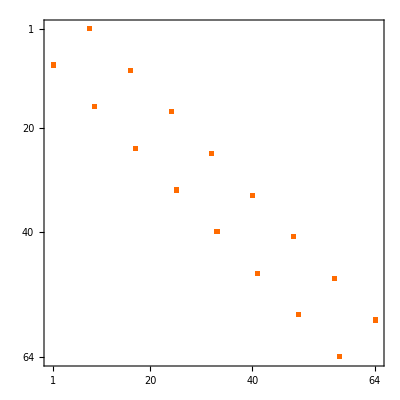
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[PlaA],MatrixPlot[PlaB],MatrixPlot[Pla]}
```

```mathematica
(* Unitaries *)
```

```mathematica
Ht[a_,b_,c_]:=a H1+b El +c Pla
```

```mathematica
PlaUniExact[t_]:=IdentityMatrix[2^6]+Sum[(ⅈ*t)^n MatrixPower[Ht[1,1,1],n]/(n!),{n,1,∞}];
PlaUniH1[t_]:=IdentityMatrix[2^6]+Sum[(ⅈ*t)^n MatrixPower[Ht[1,0,0],n]/(n!),{n,1,∞}]//FullSimplify;
PlaUniEl[t_]:=IdentityMatrix[2^6]+Sum[(ⅈ*t)^n MatrixPower[Ht[0,1,0],n]/(n!),{n,1,∞}]//FullSimplify;
PlaUniPla[t_]:=IdentityMatrix[2^6]+Sum[(ⅈ*t)^n MatrixPower[Ht[0,0,1],n]/(n!),{n,1,∞}]//FullSimplify;
```

```mathematica
State[0]=({{1.0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
```

```mathematica
(* Define our parameters for Suzuki-Trotterizing *)
```

```mathematica
DeltaT=1.0;
n=5;
steps=10;
```

```mathematica
(* Do-while below time-evolves Δt in time starting from |State[0]>. E.g. |State[1]>=[Subscript[U, A](Δt/n)Subscript[U, B](Δt/n)]^n|State[0]>, |State[2]>=[Subscript[U, A](Δt/n)Subscript[U, B](Δt/n)]^n|State[1]>, etc. *)
```

```mathematica
expr[i_]:=Defer[State[i]=MatrixPower[PlaUniH1[DeltaT/n].PlaUniEl[DeltaT/n].PlaUniPla[DeltaT/n],n].State[i-1]]
Do[expr[i][[1]],{i,steps}]
```

```mathematica
(* Take our states and measure them against the original <State[0]| to see how evolved *)
```

```mathematica
expr1[i_,j_]:=Defer[ss[i]=Transpose[State[j]].State[i]]
Do[expr1[i,0][[1]],{i,0,steps}]
```

```mathematica
trott2=Table[{i*DeltaT,Re[ss[i]][[1]][[1]]},{i,0,steps}];
```

```mathematica
trott3=Table[{i*DeltaT,Re[ss[i]][[1]][[1]]},{i,0,steps}];
```

```mathematica
trott4=Table[{i*DeltaT,Re[ss[i]][[1]][[1]]},{i,0,steps}];
```

```mathematica
trott5=Table[{i*DeltaT,Re[ss[i]][[1]][[1]]},{i,0,steps}];
```

```mathematica
Exact=Transpose[State[0]].PlaUniExact[t].State[0];
```

```mathematica
Exact/.t->2.0//Simplify
```

{{0.27377-0.0530677 ⅈ}}

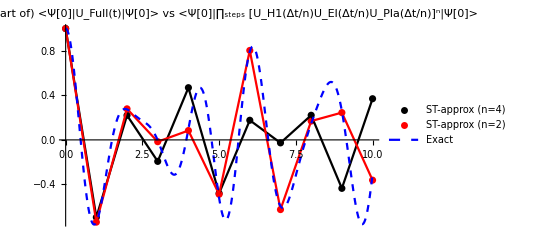

```mathematica
Show[ListPlot[{trott2,trott5},PlotStyle->{Black,Red},PlotLegends->{"ST-approx (n=4)","ST-approx (n=2)"}],ListLinePlot[{ trott2,trott5},PlotStyle->{Black,Red}],Plot[Re[Exact],{t,0,10},PlotRange->All,PlotStyle->{Blue,Dashed},PlotLegends->{"Exact"}],PlotLabel->"(Real part of)     <Ψ[0]|U_Full(t)|Ψ[0]>   vs   <Ψ[0]|∏_steps [U_H1(Δt/n)U_El(Δt/n)U_Pla(Δt/n)]^n|Ψ[0]>"]
```

```mathematica
(*** Run this all together ***)
```

```mathematica
DeltaT=1.0;
n=2;
steps=10;
expr[i_]:=Defer[State[i]=MatrixPower[PlaUniH1[DeltaT/n].PlaUniEl[DeltaT/n].PlaUniPla[DeltaT/n],n].State[i-1]]
Do[expr[i][[1]],{i,steps}]
expr1[i_,j_]:=Defer[ss[i]=Transpose[State[j]].State[i]]
Do[expr1[i,0][[1]],{i,0,steps}]
 trott2=Table[{i*DeltaT,Re[ss[i]][[1]][[1]]},{i,0,steps}];
```

```mathematica
DeltaT=1.0;
n=5;
steps=10;
expr[i_]:=Defer[State[i]=MatrixPower[PlaUniH1[DeltaT/n].PlaUniEl[DeltaT/n].PlaUniPla[DeltaT/n],n].State[i-1]]
Do[expr[i][[1]],{i,steps}]
expr1[i_,j_]:=Defer[ss[i]=Transpose[State[j]].State[i]]
Do[expr1[i,0][[1]],{i,0,steps}]
trott5=Table[{i*DeltaT,Re[ss[i]][[1]][[1]]},{i,0,steps}];
```

```mathematica
Show[ListPlot[{trott2,trott5},PlotStyle->{Black,Red},PlotLegends->{"ST-approx (n=4)","ST-approx (n=2)"}],ListLinePlot[{ trott2,trott5},PlotStyle->{Black,Red}],Plot[Re[Exact],{t,0,10},PlotRange->All,PlotStyle->{Blue,Dashed},PlotLegends->{"Exact"}],PlotLabel->"(Real part of)     <Ψ[0]|U_Full(t)|Ψ[0]>   vs   <Ψ[0]|∏_steps [U_H1(Δt/n)U_El(Δt/n)U_Pla(Δt/n)]^n|Ψ[0]>"]
```

-Graphics-